```mathematica
Clear["Global`*"]
(* Set precision to 16 digits for notebook *)
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`16."&);
```

```mathematica
(* Functions to form Butcher matrices/vectors given coefficients. S# stands for #-order SDIRK, where the diagonal entry is given first in the parameters, and D# stands for #-order DIRK. *)
S1[ad_]:={{ad}};
S2[ad_,a21_] :={{ad,0},{a21,ad}};
D2[a11_,a21_,a22_] :={{a11,0},{a21,a22}};
S3[ad_,a21_,a31_,a32_] :={{ad,0,0},{a21,ad,0},{a31,a32,ad}};
D3[a11_,a21_,a22_,a31_,a32_,a33_] :={{a11,0,0},{a21,a22,0},{a31,a32,a33}};
S4[ad_,a21_,a31_,a32_,a41_,a42_,a43_] :={{ad,0,0,0},{a21,ad,0,0},{a31,a32,ad,0},{a41,a42,a43,ad}};
D4[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_] :={{a11,0,0,0},{a21,a22,0,0},{a31,a32,a33,0},{a41,a42,a43,a44}};
S5[ad_,a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_] :={{ad,0,0,0,0},{a21,ad,0,0,0},{a31,a32,ad,0,0},{a41,a42,a43,ad,0},{a51,a52,a53,a54,ad}};
D5[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_,a51_,a52_,a53_,a54_,a55_] :={{a11,0,0,0,0},{a21,a22,0,0,0},{a31,a32,a33,0,0},{a41,a42,a43,a44,0},{a51,a52,a53,a54,a55}};
S6[ad_,a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_,a61_,a62_,a63_,a64_,a65_] :={{ad,0,0,0,0,0},{a21,ad,0,0,0,0},{a31,a32,ad,0,0,0},{a41,a42,a43,ad,0,0},{a51,a52,a53,a54,ad,0},{a61,a62,a63,a64,a65,ad}};
D6[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_,a51_,a52_,a53_,a54_,a55_,a61_,a62_,a63_,a64_,a65_,a66_] :={{a11,0,0,0,0,0},{a21,a22,0,0,0,0},{a31,a32,a33,0,0,0},{a41,a42,a43,a44,0,0},{a51,a52,a53,a54,a55,0},{a61,a62,a63,a64,a65,a66}};
E1:={{0.0}};
E2[a21_] :={{0,0},{a21,0}};
E3[a21_,a31_,a32_] :={{0,0,0},{a21,0,0},{a31,a32,0}};
E4[a21_,a31_,a32_,a41_,a42_,a43_] :={{0,0,0,0},{a21,0,0,0},{a31,a32,0,0},{a41,a42,a43,0}};
E5[a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_] :={{0,0,0,0,0},{a21,0,0,0,0},{a31,a32,0,0,0},{a41,a42,a43,0,0},{a51,a52,a53,a54,0}};
E6[a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_,a61_,a62_,a63_,a64_,a65_] :={{0,0,0,0,0,0},{a21,0,0,0,0,0},{a31,a32,0,0,0,0},{a41,a42,a43,0,0,0},{a51,a52,a53,a54,0,0},{a61,a62,a63,a64,a65,0}};
b1[bb1_]:={{bb1}};
b2[bb1_,bb2_]:={{bb1,bb2}};
b3[bb1_,bb2_,bb3_]:={{bb1,bb2,bb3}};
b4[bb1_,bb2_,bb3_,bb4_]:={{bb1,bb2,bb3,bb4}};
b5[bb1_,bb2_,bb3_,bb4_,bb5_]:={{bb1,bb2,bb3,bb4,bb5}};
b6[bb1_,bb2_,bb3_,bb4_,bb5_,bb6_]:={{bb1,bb2,bb3,bb4,bb5,bb6}};

(* Function to select Runge-Kutta Scheme and build Butcher Tableaux *)
GetButcher[type_,p_,stable_,s_,ver_]:= (
Which[type=="SDIRK" && p==1, (
(* A/L-stable, p=1, s=1 (Backward Euler) *)
A0 = S1[1.0];
b0 = b1[1.0]; ),
(* SDIRK L-stable, p=2, s=2 *)
type=="SDIRK" && stable=="L" && p==2, (
gamma=1.0-1.0/Sqrt[2.0];
A0 = S2[gamma,1.0-gamma];
b0=b2[1.0-gamma,gamma]; ),
(* SDIRK L-stable, p=3, s=3 *)
type=="SDIRK" && stable=="L" && p==3, (
q=0.435866521508458999416019;
r=1.20849664917601007033648;
z=0.717933260754229499708010;
A0 = S3[q,z-q,r,1.0-q-r];
b0=b3[r,1.0-q-r,q]; ),
(* SDIRK L-stable, p=4, s=5 *)
type=="SDIRK" && stable=="L" && p==4,(
A0=S5[0.25,0.5,17.0/50.0,-1.0/25.0,371.0/1360.0,-137.0/2720.0,15.0/544.0,25.0/24.0,-49.0/48.0,125.0/16.0,-85.0/12.0];
b0=b5[25.0/24.0,-49.0/48.0,125.0/16.0,-85.0/12.0,0.25]; ),

(* SDIRK A-stable, p=2, s=1 *)
type=="SDIRK" && stable=="A" && p==2, (
A0 = S1[0.5];
b0=b1[1.0]; ),
(* SDIRK A-stable, p=3, s=2 - Carpenter (223) *)
type=="SDIRK" && stable=="A" && p==3,(
g=(3.0+Sqrt[3.0])/6.0;
A0 = S2[g,1.0-2.0*g];
b0=b2[0.5,0.5]; ),
(* SDIRK A-stable, p=4, s=3 - Carpenter (232) *)
type=="SDIRK" && stable=="A" && p==4,(
q=1.0/Sqrt[3.0]*Cos[Pi/18.0]+0.5;
r=1.0/(6.0*(2.0*q-1.0)*(2.0*q-1.0));
A0=S3[q,0.5-q,2.0*q,1.0-4.0];
b0=b3[r,1.0-2.0*r,r]; ),


(* ESDIRK A-stable, p=2, s=2 (trap rule) *)
type=="ESDIRK" && stable=="A" && p==2, (
A0 = D2[0.0,0.5,0.5];
b0=b2[0.5,0.5]; ),
(* ESDIRK L-stable, p=2, s=3 - Carpenter 4.1.1 *)
type=="ESDIRK" && stable=="L" && p==2 , (
gamma=(2.0 - Sqrt[2.0])/2.0;
q2 = (1−2.0*gamma)/(4.0*gamma);
A0=D3[0.0,gamma,gamma,1-q2-gamma,q2,gamma];
b0=b3[1-q2-gamma,q2,gamma];
),
(* ESDIRK A-stable, p=3, s=3 - Carpenter 4.2.1 *)
type=="ESDIRK" && stable=="A" && p==3 && s==3, (
gamma=(3.0 + Sqrt[3.0])/6.0;
c3=1.0;    (*Stiffly accurate, A-stable*)
a32=c3*(c3-2*gamma)/(4.0*gamma);
q2=(3.0*c3-2.0)/(12*gamma*(c3-2*gamma));
q3=(1.0-3*gamma)/(3*c3*(c3-2*gamma));
A0=D3[0.0,gamma,gamma,c3-a32-gamma,a32,gamma];
b0=b3[1-q2-q3,q2,q3];
),


(* Gauss-Legendre, p=4 *)
type == "Gauss" && p==4, (
A0 = {{1/4.0,1/4.0-Sqrt[3.0]/6},{1/4.0+Sqrt[3.0]/6,1/4.0}};
b0 = b2[0.5,0.5];
),
type == "Gauss" && p==6, (
A0 = {{5.0/36.0,2.0/9-Sqrt[15.0]/15,5.0/36-Sqrt[15.0]/30},{5.0/36+Sqrt[15.0]/24,2.0/9,5.0/36-Sqrt[15.0]/24},{5.0/36+Sqrt[15.0]/30,2.0/+Sqrt[15.0]/15,5.0/36.0}};
b0 = b3[5.0/18.0,4.0/9.0,5.0/18.0];
),

(* Lobatto IIIA methods (A-stable) *)
type=="Lob3A" && p==2, (
A0={{0,0},{0.5,0.5}};
b0=b2[0.5,0.5];
),
type=="Lob3A" && p==4, (
A0={{0,0,0},{5.0/24,1.0/3,-1.0/24},{1.0/6,2.0/3,1.0/6}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
(* Lobatto IIIB methods (A-stable) *)
type=="Lob3B" && p==2, (
A0={{0.5,0},{0.5,0}};
b0=b2[0.5,0.5];
),
type=="Lob3B" && p==4, (
A0={{1.0/6.0,-1.0/6,0},{1.0/6,1.0/3,0},{1.0/6,5.0/6,0}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
(* Lobatto IIIC methods (L-stable) *)
type=="Lob3C" && p==2, (
A0={{0.5,-0.5},{0.5,0.5}};
b0=b2[0.5,0.5];
),
type=="Lob3C" && p==4, (
A0={{1.0/6.0,-1.0/3,1.0/6},{1.0/6,5.0/12,-1.0/12},{1.0/6,2.0/3,1.0/6}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
type=="Lob3C" && p==6, (
A0={{1.0/12,-Sqrt[5.0]/12,Sqrt[5.0]/12,-1.0/12},{1.0/12,1.0/4,(10-7*Sqrt[5.0])/60,Sqrt[5.0]/60},{1.0/12,(10+7*Sqrt[5.0])/60,1.0/4,-Sqrt[5.0]/60},{1.0/12,5.0/12,5.0/12,1.0/12}};
b0=b4[1.0/12,5.0/12,5.0/12,1.0/12];
),
(* Lobatto IIID methods (L-stable) This may night be right? *)
type=="Lob3D" && p==2, (
A0={{0.5,0.5},{-0.5,0.5}};
b0=b2[0.5,0.5];
),
type=="Lob3D" && p==4, (
A0={{1.0/6.0,0,-1.0/6},{1.0/12,5.0/12,0},{1.0/2,1.0/3,1.0/6}};
b0=b3[1.0/6,2.0/3,1.0/6];
),
(* Radau 2A methods (L-stable)*)
qrad[n_,x_]:=LegendreP[n,2*x-1]-LegendreP[n-1,2*x-1];
crad[n_]:=(x/.NSolve[qrad[n,x]==0,x])//Re //(Sort[#,Less]&);
lrad[n_,k_,x_] :=qrad[n,x]/((x-crad[n][[k]]) (D[qrad[n,x],x]/.x->crad[n][[k]]));
arad[n_,i_,k_]:= NIntegrate[lrad[n,k,x],{x,0,crad[n][[i]]}];
AR[n_]:=Table[arad[n,i,k],{i,1,n},{k,1,n}];

type == "Radau" && p == 3, (
A0 = {{5.0/12,-1.0/12},{3.0/4,1.0/4}};
b0 = b2[3.0/4,1.0/4];
),
type == "Radau" && p == 5, (
A0 = {{11.0/45-7*Sqrt[6.0]/360, 37.0/225 - 169*Sqrt[6.0]/1800,-2.0/225+Sqrt[6.0]/75},{37.0/225+169*Sqrt[6.0]/1800, 11.0/45+7*Sqrt[6.0]/360,-2.0/225-Sqrt[6.0]/75},{4.0/9-Sqrt[6.0]/36,4.0/9+Sqrt[6.0]/36,1.0/9}};
b0 = b3[4.0/9-Sqrt[6.0]/36,4.0/9+Sqrt[6.0]/36,1.0/9];
),
type == "Radau" && p == 7, (
A0 = AR[4];
b0 = b4[A0[[4,1]],A0[[4,2]],A0[[4,3]],A0[[4,4]]];
),
type == "Radau" && p == 9, (
A0 = AR[5];
b0 = b5[A0[[5,1]],A0[[5,2]],A0[[5,3]],A0[[5,4]],A0[[5,5]]];
),
type == "Radau" && p == 11, (
A0 = AR[6];
b0 =b6[A0[[6,1]],A0[[6,2]],A0[[6,3]],A0[[6,4]],A0[[6,5]],A0[[6,6]]];
),

(* ERK, p=1 (forward Euler) *)
type=="ERK" && p==1,(
A0={{0.0}};
b0=b1[1.0]; ),
(* ERK, p=2 *)
type=="ERK" && p==2,(
A0=E2[1.0];
b0=b2[0.5,0.5]; ),
(* ERK, p=3 *)
type=="ERK" && p==3,(
A0=E3[0.5,-1.0,2.0];
b0=b3[1.0/6.0,2.0/3.0,1.0/6.0]; ),
(* ERK, p=4 *)
type=="ERK" && p==4, (
A0=E4[0.5,0.0,0.5,0.0,0.0,1.0];
b0=b4[1.0/6.0,1.0/3.0,1.0/3.0,1.0/6.0]; ),
(* ERK, p=5, v1 *)
type=="ERK" && p==5 && ver==1, (
A0=E6[0.25,0.125,0.125,0,0,0.5,3.0/16.0,-0.375,0.375,9.0/16.0,-3.0/7.0,8.0/7.0,6.0/7.0,-12.0/7.0,8.0/7.0];
b0=b6[7.0/90.0,0.0,16.0/45.0,2.0/15.0,16.0/45.0,7.0/90.0]; ),
(* ERK, p=5, v2 *)
type=="ERK" && p==5 && ver==2, (
A0=E6[1.0/3.0,4.0/25.0,6.0/25.0,1.0/4.0,-3.0,15.0/4.0,2.0/27.0,10.0/9.0,-50.0/81.0,8.0/81.0,2.0/25.0,12.0/25.0,2.0/15.0,8.0/75.0,0.0];
b0=b6[23.0/192.0,0.0,125.0/192.0,0.0,-27.0/64.0,125.0/192.0]; )
];
Return [{A0,b0}];
);

(* Functions to compute lambda^k and mu^k as a function of A, k, and dt*xi, for spatial eigenvaue xi *)
lambdak[x_,k_,A_,b_]:=(1.0-x*b.Inverse[IdentityMatrix[Dimensions[A][[1]]]+x*A].ConstantArray[1.0,{Dimensions[A][[1]],1}])[[1,1]]^k;
mu[x_,k_,A_,b_]:=1.0-(k*x*b.Inverse[IdentityMatrix[Dimensions[A][[1]]]+k*x*A].ConstantArray[1.0,{Dimensions[A][[1]],1}])[[1,1]];
phiF[x_,k_,A_,b_]:=Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / (1.0 - Abs[mu[x,k,A,b]]);
phiFCF[x_,k_,A_,b_]:=Abs[lambdak[x,k,A,b]]*Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / (1.0 - Abs[mu[x,k,A,b]]);
phiFn[x_,k_,A_,b_,c_]:=Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / Sqrt[(1.0 - Abs[mu[x,k,A,b]])^2 + Abs[mu[x,k,A,b]]*Pi^2/(6*nc^2)];
phiFCFn[x_,k_,A_,b_,nc_]:=Abs[lambdak[x,k,A,b]]*Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / Sqrt[(1.0 - Abs[mu[x,k,A,b]])^2 + Abs[mu[x,k,A,b]]*Pi^2/(6*nc^2)];
phiFdiff[x_,k_,Af_,bf_,Ac_,bc_]:=Abs[lambdak[x,k,Af,bf]-mu[x,k,Ac,bc]] / (1.0 - Abs[mu[x,k,Ac,bc]]);
phiFCFdiff[x_,k_,Af_,bf_,Ac_,bc_]:=Abs[lambdak[x,k,Af,bf]]*Abs[lambdak[x,k,Af,bf]-mu[x,k,Ac,bc]] / (1.0 - Abs[mu[x,k,Ac,bc]]);
exact[x_,k_]:=Exp[-x*k];
prec[x_,Af_,Ac_]:=Abs[Eigenvalues[Inverse[IdentityMatrix[Dimensions[Ac][[1]]]+x*Ac].(IdentityMatrix[Dimensions[Af][[1]]]+x*Af)]];

linethick=0.0035;
fontsize=14;
```

(0.166667 | -0.333333 | 0.166667
0.166667 | 0.416667 | -0.0833333
0.166667 | 0.666667 | 0.166667)

(0.292893 | 0
0.707107 | 0.292893)

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

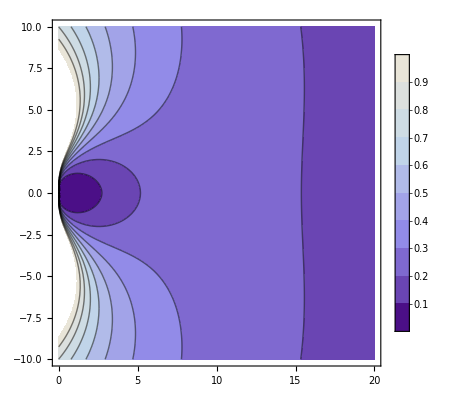

```mathematica
(* Plot convergence as function of dt*xi for k=2,4,8,16,64, with *different* RK schemes *)
butcher = GetButcher["Lob3C",4,"L",3,1];
Af=butcher[[1]];
bf=butcher[[2]];
butcherC = GetButcher["SDIRK",2,"L",2,1];
Ac=butcherC[[1]];
bc=butcherC[[2]];
Af //MatrixForm
Ac //MatrixForm
axislim = 10;
k=1;
pf=ContourPlot[phiFdiff[x+ⅈ y ,k,Af,bf,Ac,bc,1.0],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,1.0},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];Show[pf]
```

```mathematica
phiFdiff[0.025+ⅈ 0.0 ,k,Af,bf,Ac,bc,1.0]
```

0.285081

```mathematica
(* Plot preconditioning of stage matrix \Phi for one RK scheme with a different.
This is *not* MGRIT convergence. *)
butcher = GetButcher["Radau",3,"A",3,1];
Af=butcher[[1]];
bf=butcher[[2]];
butcherC = GetButcher["SDIRK",4,"L",3,1];
Ac=butcherC[[1]];
(*Ac= {{Af[[1,1]],0,0},{Af[[2,1]],Af[[2,2]],0},{Af[[3,1]],Af[[3,2]],Af[[3,3]]}};*)
bc=butcherC[[2]];
Af //MatrixForm
Ac //MatrixForm
Eigenvalues[Inverse[Ac].Af]
axislim = 10;
zlim = 2.0;
pf1=ContourPlot[prec[x+ⅈ y ,Af,Ac][[1]],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,zlim},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];
pf2=ContourPlot[prec[x+ⅈ y ,Af,Ac][[2]],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,zlim},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];
pf3=ContourPlot[prec[x+ⅈ y ,Af,Ac][[3]],{x,0,2*axislim},{y,-axislim,axislim},ColorFunction->"LakeColors",PlotRange->{0,zlim},PlotLegends->Automatic,Exclusions->{0,0},PlotPoints->50 ,PlotRangePadding->0];
Show[pf1]
Show[pf2]
Show[pf3]
```

(0.416667 | -0.0833333
0.75 | 0.25)

(0.25 | 0 | 0 | 0 | 0
0.5 | 0.25 | 0 | 0 | 0
0.34 | -0.04 | 0.25 | 0 | 0
0.272794 | -0.0503676 | 0.0275735 | 0.25 | 0
1.04167 | -1.02083 | 7.8125 | -7.08333 | 0.25)

Dot::dotsh: Tensors {{4.,0.,0.,0.,0.},{-8.,4.,4.32072×10^-16,1.6694×10^-15,-1.32146×10^-16},{«1»},{-5.23529,0.735294,-0.441176,4.,-4.21702×10^-17},{12.3333,17.1667,-137.5,113.333,4.}} and {{0.416667,-0.0833333},{0.75,0.25}} have incompatible shapes.

Eigenvalues[{{4.,0.,0.,0.,0.},{-8.,4.,4.32072×10^-16,1.6694×10^-15,-1.32146×10^-16},{-6.72,0.64,4.,1.57399×10^-15,-8.63309×10^-17},{-5.23529,0.735294,-0.441176,4.,-4.21702×10^-17},{12.3333,17.1667,-137.5,113.333,4.}}.{{0.416667,-0.0833333},{0.75,0.25}}]

Dot::dotsh: Tensors {«1»} and {{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},{0.000306122-7.49969 ⅈ,1.0001-2.4999 ⅈ}} have incompatible shapes.

Dot::dotsh: Tensors {{0.147657+0.334918 ⅈ,-5.35309×10^-17-2.20588×10^-17 ⅈ,-4.26115×10^-16-1.00407×10^-15 ⅈ,2.02781×10^-17+1.55885×10^-16 ⅈ,-3.16348×10^-18+2.24164×10^-17 ⅈ},«4»} and {{1.17024-4.1665 ⅈ,-0.0340476+0.833299 ⅈ},{0.306429-7.49969 ⅈ,1.10214-2.4999 ⅈ}} have incompatible shapes.

Dot::dotsh: Tensors {{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«3»,{0.922891-0.616996 ⅈ,«3»,0.156397+0.324681 ⅈ}} and {{1.34031-4.1665 ⅈ,-0.0680612+0.833299 ⅈ},{0.612551-7.49969 ⅈ,1.20418-2.4999 ⅈ}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {«1»} and {{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},{0.000306122-7.49969 ⅈ,1.0001-2.4999 ⅈ}} have incompatible shapes.

Part::partw: Part 2 of Abs[Eigenvalues[«1».{{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},{0.000306122-7.49969 ⅈ,1.0001-2.4999 ⅈ}}]] does not exist.

Dot::dotsh: Tensors {{0.147657+0.334918 ⅈ,-5.35309×10^-17-2.20588×10^-17 ⅈ,-4.26115×10^-16-1.00407×10^-15 ⅈ,2.02781×10^-17+1.55885×10^-16 ⅈ,-3.16348×10^-18+2.24164×10^-17 ⅈ},«4»} and {{1.17024-4.1665 ⅈ,-0.0340476+0.833299 ⅈ},{0.306429-7.49969 ⅈ,1.10214-2.4999 ⅈ}} have incompatible shapes.

Part::partw: Part 2 of Abs[Eigenvalues[{{0.147657+0.334918 ⅈ,-5.35309×10^-17-2.20588×10^-17 ⅈ,-4.26115×10^-16-1.00407×10^-15 ⅈ,2.02781×10^-17+1.55885×10^-16 ⅈ,-3.16348×10^-18+2.24164×10^-17 ⅈ},«3»,{1.01008-0.629042 ⅈ,«3»,0.147657+0.334918 ⅈ}}.«1»]] does not exist.

Dot::dotsh: Tensors {{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«3»,{0.922891-0.616996 ⅈ,«3»,0.156397+0.324681 ⅈ}} and {{1.34031-4.1665 ⅈ,-0.0680612+0.833299 ⅈ},{0.612551-7.49969 ⅈ,1.20418-2.4999 ⅈ}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Part::partw: Part 2 of Abs[Eigenvalues[{{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«3»,{0.922891-0.616996 ⅈ,«3»,0.156397+0.324681 ⅈ}}.«1»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::dotsh: Tensors {«1»} and {{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},{0.000306122-7.49969 ⅈ,1.0001-2.4999 ⅈ}} have incompatible shapes.

Part::partw: Part 3 of Abs[Eigenvalues[«1».{{1.00017-4.1665 ⅈ,-0.0000340136+0.833299 ⅈ},{0.000306122-7.49969 ⅈ,1.0001-2.4999 ⅈ}}]] does not exist.

Dot::dotsh: Tensors {{0.147657+0.334918 ⅈ,-5.35309×10^-17-2.20588×10^-17 ⅈ,-4.26115×10^-16-1.00407×10^-15 ⅈ,2.02781×10^-17+1.55885×10^-16 ⅈ,-3.16348×10^-18+2.24164×10^-17 ⅈ},«4»} and {{1.17024-4.1665 ⅈ,-0.0340476+0.833299 ⅈ},{0.306429-7.49969 ⅈ,1.10214-2.4999 ⅈ}} have incompatible shapes.

Part::partw: Part 3 of Abs[Eigenvalues[{{0.147657+0.334918 ⅈ,-5.35309×10^-17-2.20588×10^-17 ⅈ,-4.26115×10^-16-1.00407×10^-15 ⅈ,2.02781×10^-17+1.55885×10^-16 ⅈ,-3.16348×10^-18+2.24164×10^-17 ⅈ},«3»,{1.01008-0.629042 ⅈ,«3»,0.147657+0.334918 ⅈ}}.«1»]] does not exist.

Dot::dotsh: Tensors {{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«3»,{0.922891-0.616996 ⅈ,«3»,0.156397+0.324681 ⅈ}} and {{1.34031-4.1665 ⅈ,-0.0680612+0.833299 ⅈ},{0.612551-7.49969 ⅈ,1.20418-2.4999 ⅈ}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Part::partw: Part 3 of Abs[Eigenvalues[{{0.156397+0.324681 ⅈ,3.21032×10^-17+5.42166×10^-17 ⅈ,-2.14587×10^-16-9.72018×10^-17 ⅈ,2.35906×10^-16+1.34194×10^-16 ⅈ,3.2543×10^-18-9.90671×10^-18 ⅈ},«3»,{0.922891-0.616996 ⅈ,«3»,0.156397+0.324681 ⅈ}}.«1»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*butcher = GetButcher["SDIRK",6,"L",3,1];*)
butcher = GetButcher["Radau",7,"A",3,1];
A=butcher[[1]];
b=butcher[[2]];
A //MatrixForm
b //MatrixForm
Inverse[A]//MatrixForm
Eigenvalues[Inverse[A]]
b.Inverse[A]
```

(0.112999 | -0.0403092 | 0.0258024 | -0.00990468
0.234384 | 0.206893 | -0.0478571 | 0.0160474
0.216682 | 0.406123 | 0.189037 | -0.0241821
0.220462 | 0.388193 | 0.328844 | 0.0625)

(0.220462 | 0.388193 | 0.328844 | 0.0625)

(5.64411 | 1.92351 | -0.585901 | 0.173878
-5.04921 | 1.2211 | 1.75468 | -0.434791
3.49247 | -3.98452 | 0.634792 | 1.82214
-6.92349 | 6.59524 | -12.1717 | 8.5)

{3.21281+4.77309 ⅈ,3.21281-4.77309 ⅈ,4.78719+1.56748 ⅈ,4.78719-1.56748 ⅈ}

{{-3.33067×10^-16,2.77556×10^-16,-4.44089×10^-16,1.}}

```mathematica
(* Column sums of adjugate matrix *)
s = Flatten[Dimensions[Transpose[b],1]][[1]];
sc = ConstantArray[0,{1,s}];
sc[[1,s]]=1;
sc.{{"[◼]", "Adjugate"}}[A - xx*IdentityMatrix[Length[A]]]
Total[{{"[◼]", "Adjugate"}}[A - xx*IdentityMatrix[Length[A]]],{2}]
{{"[◼]", "Adjugate"}}[A - xx*IdentityMatrix[Length[A]]]
```

{{-0.00824225-0.0749535 xx-0.220462 xx^2,0.00785147-0.00741627 xx-0.388193 xx^2,-0.0144902+0.118084 xx-0.328844 xx^2,0.010119-0.107143 xx+0.508929 xx^2-xx^3}}

{0.00851856-0.0961594 xx+0.482841 xx^2-xx^3,-0.00298598+0.00729237 xx+0.161962 xx^2-xx^3,0.00233914-0.00296974 xx-0.216231 xx^2-xx^3,-0.0047619-0.0714286 xx-0.428571 xx^2-xx^3}

{{0.00671918-0.0850144 xx+0.458429 xx^2-xx^3,0.00228989-0.0167733 xx+0.0403092 xx^2,-0.000697502+0.00827898 xx-0.0258024 xx^2,0.000206998-0.00265073 xx+0.00990468 xx^2},{-0.00601097+0.0657881 xx-0.234384 xx^2,0.00145369-0.0447831 xx+0.364536 xx^2-xx^3,0.00208891-0.0197237 xx+0.0478571 xx^2,-0.000517609+0.00601111 xx-0.0160474 xx^2},{0.0041577-0.0314851 xx-0.216682 xx^2,-0.00474347+0.089396 xx-0.406123 xx^2,0.000755705-0.0487739 xx+0.382392 xx^2-xx^3,0.00216921-0.0121067 xx+0.0241821 xx^2},{-0.00824225-0.0749535 xx-0.220462 xx^2,0.00785147-0.00741627 xx-0.388193 xx^2,-0.0144902+0.118084 xx-0.328844 xx^2,0.010119-0.107143 xx+0.508929 xx^2-xx^3}}

```mathematica
(* Determinants and adjugates *)
ResourceFunction["Adjugate"]
M2 = {{m11-x,m12},{m21,m22-y}};
M2c = {{m11-xx,m12},{m21,m22-xx}};
A2 = {{m11,m12},{m21,m22}};
M3 = {{m11-xx,m12,m13},{m21,m22-yy,m23},{m31,m32,m33-zz}};
M3c = {{m11-xx,m12,m13},{m21,m22-xx,m23},{m31,m32,m33-xx}};
A3 = {{m11,m12,m13},{m21,m22,m23},{m31,m32,m33}};
M4 = {{m11-xx,m12,m13,m14},{m21,m22-yy,m23,m24},{m31,m32,m33-zz,m34},{m41,m42,m43,m44-qq}};
M4c = {{m11-xx,m12,m13,m14},{m21,m22-xx,m23,m24},{m31,m32,m33-xx,m34},{m41,m42,m43,m44-xx}};
M5c = {{m11-xx,m12,m13,m14,m15},{m21,m22-xx,m23,m24,m25},{m31,m32,m33-xx,m34,m35},{m41,m42,m43,m44-xx,m45},{m51,m52,m53,m54,m55-xx}};
A4 = {{m11,m12,m13,m14},{m21,m22,m23,m24},{m31,m32,m33,m34},{m41,m42,m43,m44}};
(*Simplify[{{"[◼]", "Adjugate"}}[M5c]]*)
```

[◼] | Adjugate

{{0.000579096-0.0111921 xx+0.101026 xx^2-0.482557 xx^3+xx^4,0.000191266-0.00234992 xx+0.0124338 xx^2-0.0267353 xx^3,-0.0000578827+0.001128 xx-0.00753184 xx^2+0.0186769 xx^3,0.0000264355-0.000564327 xx+0.00447959 xx^2-0.0128791 xx^3,-8.843×10^-6+0.000193475 xx-0.00161286 xx^2+0.00504284 xx^3},{-0.000473636+0.00785756 xx-0.0548895 xx^2+0.153775 xx^3,0.00011945-0.00516391 xx+0.0676685 xx^2-0.409341 xx^3+xx^4,0.000156336-0.0026212 xx+0.0161259 xx^2-0.0364446 xx^3,-0.0000572686+0.00116881 xx-0.00847061 xx^2+0.0212331 xx^3,0.0000181441-0.000385277 xx+0.00297399 xx^2-0.00793558 xx^3},{0.00027263-0.00307715 xx-0.00149123 xx^2+0.140063 xx^3,-0.000297356+0.00829856 xx-0.0823348 xx^2+0.298967 xx^3,0.0000566644-0.00355512 xx+0.0579367 xx^2-0.38797 xx^3+xx^4,0.000166556-0.00276618 xx+0.0157911 xx^2-0.0339691 xx^3,-0.0000434565+0.000834237 xx-0.00494083 xx^2+0.0109443 xx^3},{-0.000256525+0.00255971 xx+0.0346299 xx^2+0.144894 xx^3,0.000224415-0.00556909 xx+0.0115278 xx^2+0.2765 xx^3,-0.000343144+0.0104713 xx-0.0967205 xx^2+0.325798 xx^3,0.0000384413-0.00548566 xx+0.0733687 xx^2-0.426799 xx^3+xx^4,0.000185845-0.00180079 xx+0.00817831 xx^2-0.0157089 xx^3},{0.000556377+0.00856305 xx+0.055666 xx^2+0.143714 xx^3,-0.000460996-0.000390235 xx+0.0471557 xx^2+0.281356 xx^3,0.000580497-0.00179341 xx-0.0433894 xx^2+0.311827 xx^3,-0.00120498+0.0158428 xx-0.0927656 xx^2+0.223104 xx^3,0.000859788-0.0142857 xx+0.116667 xx^2-0.515556 xx^3+xx^4}}

```mathematica
butcher = GetButcher["Radau",7,"A",3,1];
A=butcher[[1]];
A //MatrixForm
comm[M_,i_,j_,k_,l_] := M[[i,j]]*M[[k,l]] - M[[k,j]]*M[[i,l]];
comm[A,1,2,2,3]
```

(0.112999 | -0.0403092 | 0.0258024 | -0.00990468
0.234384 | 0.206893 | -0.0478571 | 0.0160474
0.216682 | 0.406123 | 0.189037 | -0.0241821
0.220462 | 0.388193 | 0.328844 | 0.0625)

-0.00340924